```mathematica
Clear["Global`*"]
```

```mathematica
(* Payoffs *)
pi=x*(α*γ-x);
pi2=x*(α*h-x);
pig=x*(α*γg-x);
ψ=γ*x*(1-α);
ψ2=h*x*(1-α);
ψg=γg*x*(1-α);
```

```mathematica
(* Mean fitness *)
wh1=u*pi+(1-u)*pi2;
wh2=u*pi2+(1-u)*pi;
whg=pig;
ws1=v1*ψ+v2*ψ2+(1-v1-v2)*ψg;
ws2=v1*ψ2+v2*ψ+(1-v1-v2)*ψg;
```

```mathematica
(* Dynamics d[u,v1,v2]/dt = F shifted to the right end point of the interval *)
F={u*(1-u)*(ws1-ws2),
v1*(wh1-(v1*wh1+v2*wh2+(1-v1-v2)*whg)),
v2*(wh2-(v1*wh1+v2*wh2+(1-v1-v2)*whg))}/.{u-> u+1-(pi-pig)/(pi-pi2)};
```

```mathematica
(* The Jacobian in the desired form *)
J=Simplify[D[F,{{u,v1,v2}}]/.{u-> 0,v1-> 0,v2->0}];
```

```mathematica
(* Reduce system *)
EQ=F/.{u-> μ,v1-> y,v2-> z};
m=a20*μ^2+a11*μ*y+a02*y^2;
IC=D[m,{{μ,y}}].EQ[[1;;2]]-EQ[[3]]/.{z-> m};
```

```mathematica
Q1=Coefficient[IC/.{y->0},μ^2];
Q2=Coefficient[IC,μ*y];
Q3=Coefficient[IC/.{μ->0},y^2];
Solve[{Q1==0,Q2==0,Q3==0},{a11,a02,a20}]
```

{{a11→0,a02→0,a20→0}}

```mathematica
(* The reduced system *)
G=Simplify[EQ[[1;;2]]/.{z->0}]
```

{-(x y (-1+α) (h-γg+h μ-γ μ) (γ-γg+h μ-γ μ))/(h-γ),x (-1+y) y α (h-γ) μ}

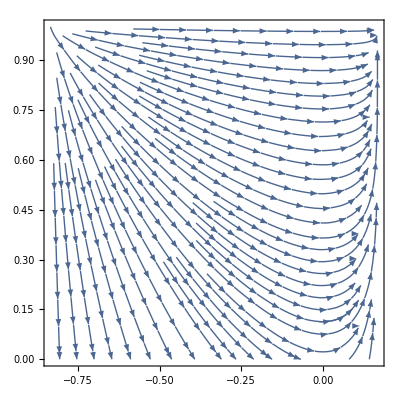

```mathematica
(* Example plotted vector field *)
VF =G/.{α->0.5,γ->1.1,γg->1,h-> 0.5,x->0.5}; 
(* bifuction point at right endpoint of interval *)
 μ2 = 1-(pi-pig)/(pi-pi2)/.{α->0.5,γ->1.1,γg->1,h-> 0.5,x->0.5} ;
StreamPlot[VF[[1;;2]],{μ,-μ2,1-μ2},{y,0,1}]
```